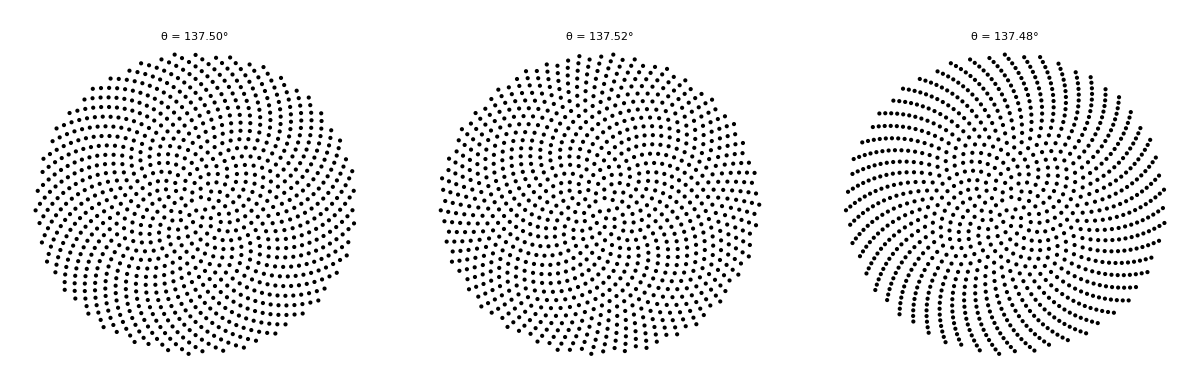

```mathematica
(*フィボナッチ構造の検証:Vogelモデルによるシミュレーション*)

nPoints=1000;rScale=0.75;angles={137.5,137.52,137.48};vogelSpiral[thetaDeg_]:=Module[{k,theta,r,pts},k=Range[nPoints];
theta=k*thetaDeg*Degree;
r=Sqrt[k];
Transpose[{r Cos[theta],r Sin[theta]}]];

plotStyle={PlotStyle->Directive[Orange,PointSize[0.008]],Axes->False,Frame->False,AspectRatio->1,PlotRange->All,Background->White};

GraphicsRow[Table[Graphics[{Point[vogelSpiral[θ]]},PlotLabel->Style[Row[{"θ = ",NumberForm[θ,{6,2}],"°"}],14,Bold],ImageSize->250],{θ,angles}],Spacings->10]
```

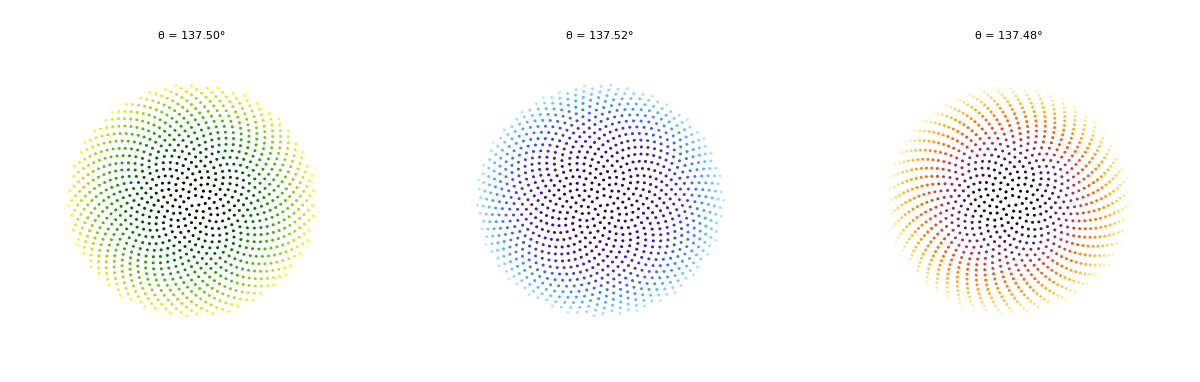

```mathematica
(*フィボナッチ構造の安定性と±0.02°ズレの崩れを可視化*)

nPoints=1000;
rScale=0.75;
angles={137.5,137.52,137.48};
colorSets={"AvocadoColors","DeepSeaColors","SunsetColors"};


vogelSpiral[thetaDeg_]:=Module[{k,theta,r},k=Range[nPoints];
theta=k*thetaDeg*Degree;
r=Sqrt[k];
Transpose[{r Cos[theta],r Sin[theta],k}]];


makePlot[θ_,colorTheme_]:=Module[{pts},pts=vogelSpiral[θ];
Graphics[Table[{EdgeForm[],ColorData[colorTheme][k/nPoints],Disk[pts[[k,1;;2]],0.4]},{k,1,nPoints}],PlotLabel->Style[Row[{"θ = ",NumberForm[θ,{6,2}],"°"}],16,Bold,Darker[Gray]],Background->White,PlotRange->{{-40,40},{-40,40}},ImageSize->300,AspectRatio->1]];

plots=MapThread[makePlot,{angles,colorSets}];

GraphicsRow[plots,Spacings->20]
```

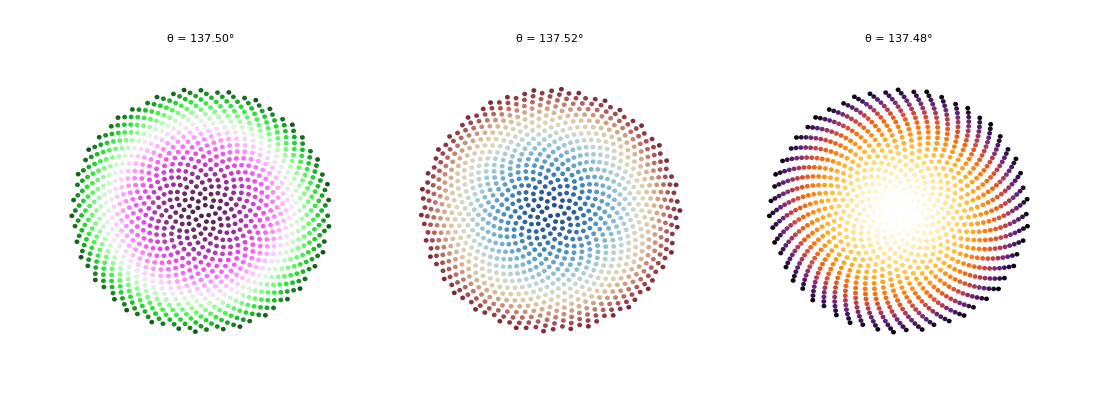

```mathematica
(*強調版フィボナッチ構造シミュレーション（Vogelモデル）*)

nPoints=1000;
angles={137.5,137.52,137.48};
colorSets={"GreenPinkTones","BlueGreenYellow","SunsetColors"};

vogelSpiral[thetaDeg_]:=Module[{k,theta,r},k=Range[nPoints];
theta=k*thetaDeg*Degree;
r=Sqrt[k];
Transpose[{r Cos[theta],r Sin[theta],k}]];


makePlot[θ_,colorTheme_,emphasize_]:=Module[{pts,alphaVal},pts=vogelSpiral[θ];
alphaVal=If[emphasize,1,0.9];(*α=透明度制御*)Graphics[Table[{EdgeForm[],ColorData[colorTheme][1-k/nPoints],Opacity[alphaVal],Disk[pts[[k,1;;2]],0.6]    },{k,1,nPoints}],PlotLabel->Style[Row[{"θ = ",NumberForm[θ,{6,2}],"°"}],20,Bold,GrayLevel[0.2]],Background->White,PlotRange->{{-40,40},{-40,40}},ImageSize->380,AspectRatio->1]];

plots={makePlot[137.5,"GreenPinkTones",False],makePlot[137.52,"RedBlueTones",True],makePlot[137.48,"SunsetColors",True]};

GraphicsRow[plots,Spacings->-50,ImageSize->1100  ]
```